# solving ODEs and PDEs

## ODEs

```mathematica
sol=NDSolve[{x''[t]+0.15x'[t]-x[t]+x[t]^3==0.3Cos[t],x[0]==-1,x'[0]==1},x,{t,0,50}]
```

{{x→InterpolatingFunction[…]}}

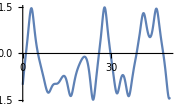

```mathematica
Plot[Evaluate[x[t]/.sol[[1]]],{t,0,50},ImageSize->Small]
```

```mathematica
(* another example *)
```

```mathematica
sol=ParametricNDSolve[{x''[t]-x'[t]+x[t]==0,x[0]==1,x'[0]==s},x,{t,0,10},{s}]
```

{x→ParametricFunction[<>]}

```mathematica
Plot3D[Evaluate[x[s][t]/.sol],{s,0,1},{t,0,10},ColorFunction->"Rainbow",PlotPoints->25,PlotRange->All]
```

-Graphics3D-

```mathematica
(* find value of s for which x -> 0 at t = 10 *)
```

```mathematica
root=FindRoot[Evaluate[x[s][10]/.sol ]==0,{s,1.}]
```

{s→1.40296}

```mathematica
val=x[s/.root][10]/.sol[[1]]
```

-2.13635×10^-13

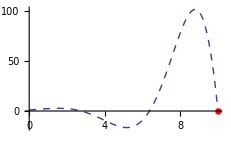

```mathematica
Show[Plot[Evaluate[x[s/.root][t]/.sol[[1]]],{t,0,10},PlotStyle->{Dashed,Thick,ColorData[1][1]}],
Graphics[{PointSize[0.02],Red,Point[{10,val}]}]]
```

## Lorenz equation

```mathematica
lsol=NDSolve[
{x'[t]==-3(x[t]-y[t]),
y'[t]==-x[t]z[t]+26.5x[t]-y[t],z'[t]==x[t]y[t]-z[t],
x[0]==z[0]==0,y[0]==1},
{x,y,z},{t,0,200},MaxSteps->∞]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],z→InterpolatingFunction[…]}}

```mathematica
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.lsol],{t,0,200},PlotPoints->150,PlotStyle->{Thickness[0.0025],ColorData[1][1]},
ImageSize->Small,Boxed->False,Axes->False]
```

-Graphics3D-

## Transient Diffusion equation

```mathematica
hsol=NDSolve[{D[u[t,x],t]==D[u[t,x],x,x],u[0,x]==0,u[t,0]==Sin[t],u[t,5]==0},u,{t,0,10},{x,0,5}]
```

{{u→InterpolatingFunction[…]}}

```mathematica
Plot3D[Evaluate[u[t,x]/.hsol[[1]]],{t,0,10},{x,0,5},PlotRange->All,ColorFunction->"Rainbow",Mesh->Full,ImageSize->Small]
```

-Graphics3D-

## Tsunami wave (shallow water equations)

## The Shallow Water Wave Equations

```mathematica
swe={D[h[λ,ϕ,t], t]+1/(R Cos[ϕ])(D[(u[λ,ϕ,t]  (h[λ, ϕ, t]   - b[λ, ϕ] )), λ]+D[(v[λ, ϕ, t]  (h[λ, ϕ, t]   - b[λ, ϕ] )Cos[ϕ]), ϕ])==0,(D[u[λ, ϕ, t], ϕ]  v[λ, ϕ, t])/R+(g D[h[λ, ϕ, t], λ])/(R Cos[ϕ])+D[u[λ, ϕ, t], t]+(u[λ, ϕ, t]  D[u[λ, ϕ, t], λ])/(R Cos[ϕ])==f v[λ, ϕ, t] ,
(D[v[λ, ϕ, t], ϕ]  v[λ, ϕ, t])/R+(g D[h[λ, ϕ, t], ϕ])/R+D[v[λ, ϕ, t], t] +(u[λ, ϕ, t]  D[v[λ, ϕ, t], λ])/(R Cos[ϕ])==-f u[λ, ϕ, t] };
```

## Shapes for Ocean Floor and Fault Displacement

```mathematica
Seamount[s_, w_, {λ_, ϕ_}][l_, p_] := s Exp[-w ((l-λ)^2 + (p-ϕ)^2)];FaultDisplacement[p1_, p2_][p_?(VectorQ[#, NumberQ]&)] :=
If[p1 == p2,Norm[p - p1],
 Module[{pp1,pp2, p12},
pp1 = p - p1;
pp2 = p - p2;
p12 = (p1 - p2)/Norm[p1 - p2];
If[Sign[p12.pp1] != Sign[p12.pp2],
Norm[pp1 - pp1.p12 p12],
Min[Norm[pp1], Norm[pp2]]]]];
```

## The Ocean Floor

```mathematica
Subscript[λ, min] =-15 ° ; Subscript[λ, max]= 15 °;Subscript[λ, e] = 0;Subscript[λ, i]= 2.5 °;
Subscript[ϕ, min]= -35 °;Subscript[ϕ, max]= 5 °;Subscript[ϕ, 1]= -10 °;Subscript[ϕ, 2]= -20 °; Subscript[ϕ, i]= -25 °;
nxy = 50;
b[λ_, ϕ_] := -4000 + Seamount[3500, 1000, {-2.5 °, -25 °}][λ, ϕ]+ Seamount[3000, 1000, {-5 °, -23 °}][λ, ϕ] +  Seamount[3000, 1000, {-7.5 °, -27 °}][λ, ϕ]+  Seamount[3000, 1000, {5°, -24°}][λ, ϕ]+Seamount[3000, 1000, {5°, -21°}][λ, ϕ]+Seamount[3000, 1000, {5°, -18°}][λ, ϕ]+Seamount[3000, 1000, {5°, -15°}][λ, ϕ]+Seamount[3000, 1000, {5°, -12°}][λ, ϕ]+
Seamount[3750, 1000, {-2°, -18°}][λ, ϕ];
```

## Solving the PDEs

```mathematica
T = 2 3600;Block[{R = 6378000, ω = (2 π)/(24 3600), f= 2ω Sin[ϕ], g = 9.8, s = .95},
sol = First[h /. NDSolve[{swe, h[λ, ϕ, 0] == Exp[-2000 (FaultDisplacement[{Subscript[λ, e],Subscript[ϕ, 1]},{Subscript[λ, e],Subscript[ϕ, 2]}][{λ,ϕ}])^2], u[λ, ϕ, 0] == 0, v[λ, ϕ, 0] == 0, h[λ, Subscript[ϕ, min], t] ==  h[λ, Subscript[ϕ, max], t], h[Subscript[λ, min], ϕ, t] ==  h[ Subscript[λ, max], ϕ, t]},h, {λ, Subscript[λ, min],  Subscript[λ, max]}, {ϕ,Subscript[ϕ, min], Subscript[ϕ, max]}, {t,0,T},DependentVariables->{h,u,v}, Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MaxPoints"->nxy, "MinPoints"->nxy, "DifferenceOrder"->"Pseudospectral"}}]]]
```

## visualize the solution

```mathematica
ani=Table[Plot3D[sol[λ, ϕ, t], {λ, Subscript[λ, min], Subscript[λ, max]}, {ϕ, Subscript[ϕ, min], Subscript[ϕ, max]}, PlotRange->{-1,1}, PlotPoints->2nxy, Mesh->None,MaxRecursion->0,PlotStyle->{RGBColor[.4,.4,1],Specularity[White,100]},
Boxed->False,Axes->None,Background->White],{t,0,T,360}];
```

```mathematica
(*Animate[ani[[i]],{i,1,Length[ani],1},DefaultDuration->0.25Length[ani],SaveDefinitions->True]*)
```

## Heat equation

```mathematica
sol=NDSolve[{
D[u[t,x,y], t]==D[u[t,x,y], x,x]+D[u[t,x,y], y,y],
u[0,x,y]==0,
u[t,x,0]==Cos[t+Pi/2],u[t,0,y]==Sin[t],
u[t,x,5]==0,u[t,5,y]==0},u,{t,0,10},{x,0,5},{y,0,5}
]
```

{{u→InterpolatingFunction[{{0., 10.}, {0., 5.}, {0., 5.}}, <>]}}

```mathematica
Manipulate[
Plot3D[Evaluate[u[t,x,y]/.sol],{x,0,5},{y,0,5},
PlotRange->{-1,1},
ColorFunctionScaling->False,ColorFunction->(ColorData["TemperatureMap"][(#3+1)/2]&)
],
{t,0,10}];
```

```mathematica
Table[
Plot3D[u[t,x,y]/.sol,{x,0,5},{y,0,5},
PlotRange->{-1,1},
ColorFunctionScaling->False,ColorFunction->(ColorData["TemperatureMap"][(#3+1)/2]&)
],{t,0,10,0.5}](*//ListAnimate[#,SaveDefinitions->True]&*)
```

## Bouncing ball ODE (WhenEvent)

```mathematica
sol=NDSolve[{
y''[t]==-9.81,y[0]==10,
y'[0]==0,
WhenEvent[y[t]==0,y'[t]->-0.7y'[t]]},y,{t,0,7}
]
```

{{y→InterpolatingFunction[…]}}

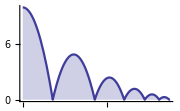

```mathematica
Plot[Evaluate[y[t]/.sol[[1]]],{t,0,7},PlotStyle->ColorData[1][1],FillingStyle->Lighter[ColorData[1][1],0.75],PlotRange->All,Filling->Axis,ImageSize->Small]
```

```mathematica
(*velocity profile*)
```

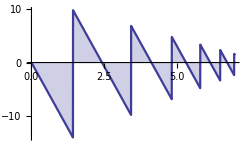

```mathematica
Plot[Evaluate[y'[t]/.sol[[1]]],{t,0,7},PlotStyle->ColorData[1][1],FillingStyle->Lighter[ColorData[1][1],0.75],PlotRange->All,Filling->Axis]
```

## Poincare section of Duffing Equation (WhenEvent)

```mathematica
data=Reap[NDSolve[{x''[t]+0.15x'[t]-x[t]+x[t]^3==0.3Cos[t],
x[0]==0,x'[0]==0,WhenEvent[Mod[t,2π]==0,Sow[{x[t],x'[t]}]]},
x,{t,0,100000},MaxSteps->∞]][[2]];
```

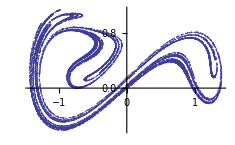

```mathematica
ListPlot[data,PlotStyle->Directive[ColorData[1][1],PointSize[0.0033]]]
```

## Vibration of a stretched string (DSolve)

```mathematica
WaveEqn=D[u[t,x], t,t]==D[u[t,x], x,x];
bc={u[t,0]==0,u[t,π]==0};
ic={u[0,x]==x^2(π-x),Derivative[1,0][u][0,x]==0};
```

```mathematica
dsol=DSolve[{WaveEqn,bc,ic},u,{t,x}]/.K[1]->m;
```

```mathematica
dsol
```

{{u→Function[{t,x},-(4 (1+2 (-1)^m) Cos[t m] Sin[x m])/m^3m1∞]}}

```mathematica
asol[t_,x_]=u[t,x]/.First[dsol]/.{∞->4}//Activate
```

4 Cos[t] Sin[x]-3/2 Cos[2 t] Sin[2 x]+4/27 Cos[3 t] Sin[3 x]-3/16 Cos[4 t] Sin[4 x]

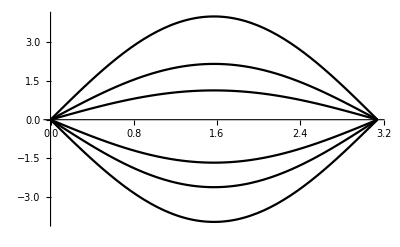
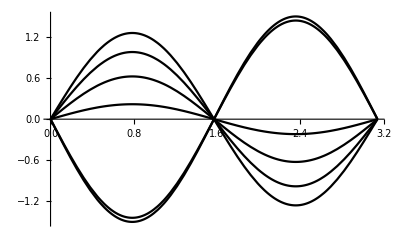
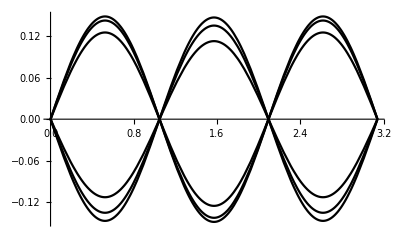
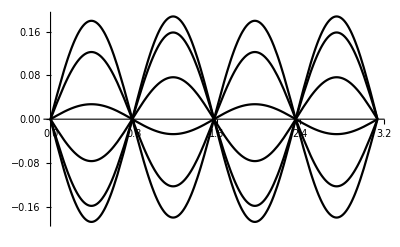

```mathematica
Table[Plot[Table[asol[t,x][[m]],{t,0,5}]//Evaluate,{x,0,π},Ticks->False,PlotStyle->{Black}],{m,4}]
```

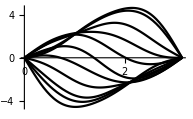

```mathematica
Plot[Table[asol[t,x],{t,0,10}]//Evaluate,{x,0,π},Ticks->False,PlotStyle->{Black}]
```

```mathematica
Animate[Plot[asol[t,x],{x,0,π},PlotRange->{-5,5},PerformanceGoal->"Speed",
ImageSize->Medium,PlotStyle->Red],{t,0,10}];
```

## Flow of heat in insulated bar (DSolve)

```mathematica
HeatEqn={D[u[t,x], t]==D[u[t,x], x,x]};
boundaryCondition={(D[u[t,x], x]/.x->0)==0,(D[u[t,x], x]/.x->1)==0};
initialCondition=u[0,x]==100-80x;
```

```mathematica
sol=DSolve[{HeatEqn,boundaryCondition,initialCondition},u[t,x],{t,x}]/.K[1]->m
```

{{u[t,x]→60+2 -(80 (-1+(-1)^m) ⅇ^(-m^2 π^2 t) Cos[m π x])/(m^2 π^2)m1∞}}

```mathematica
asol[t_,x_]=First[u[t,x]/.sol]/.{∞->6}//Activate//Expand
```

60+(320 ⅇ^(-π^2 t) Cos[π x])/π^2+(320 ⅇ^(-9 π^2 t) Cos[3 π x])/(9 π^2)+(64 ⅇ^(-25 π^2 t) Cos[5 π x])/(5 π^2)

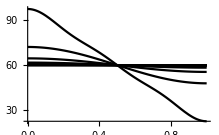

```mathematica
Plot[Table[asol[t,x],{t,0,0.9,0.1}]//Evaluate,{x,0,1},PlotRange->All,PlotStyle->Black]
```

```mathematica
Plot3D[asol[t,x],{t,0,0.9},{x,0,1},PlotPoints->50,PlotRange->All,AxesLabel->{"time","Bar"},ColorFunction->"Rainbow"]
```

-Graphics3D-

## Laplacian (NDSolve)

```mathematica
uif=NDSolveValue[{-Laplacian[u[x,y],{x,y}]==10,u[x,0]==0,u[x,1]==1},u,{x,0,1},{y,0,1}]
```

InterpolatingFunction[…]

```mathematica
Plot3D[uif[x,y],{x,0,1},{y,0,1},ColorFunction->"TemperatureMap",PlotPoints->50,Boxed->False,Axes->False,ImageSize->Small]
```

-Graphics3D-

## Parameter fitting to experimental data (ParametricNDSolve and FindFit)

```mathematica
data={
{0.5,29.5065424},{1.,39.3139096},
{1.5,57.6404457},{2.,52.9218489},
{2.5,61.8157312},{3.,72.70055773},
{3.5,89.3180532},{4.,89.10336725},
{4.5,78.9695762},{5.,92.00308382},
{5.5,65.5803180},{6.,66.15649415},
{6.5,53.7603732},{7.,46.07415774},
{7.5,26.8109925},{8.,4.692714582},
{8.5,-10.176781},{9.,-40.9309358},
{9.5,-65.430306},{10.,-79.6686718}
};
```

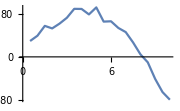

```mathematica
ListLinePlot[data,ImageSize->Small]
```

fit a differential equation of the form  y’’(t)= -w y(t), y(0)=a, y’(0)=b

```mathematica
pfun=y/.ParametricNDSolve[{y''[t]==-w y[t],y[0]==a,y'[0]==b},y,{t,0,10},{w,a,b}]
```

ParametricFunction[<>]

```mathematica
fit=FindFit[data,pfun[w,a,b][t],{{w,.1},{a,-1},{b,1}},t]
```

{w→0.154676,a→-0.269287,b→35.5332}

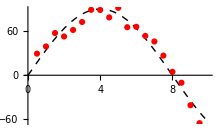

```mathematica
Plot[pfun[Sequence@@({w,a,b}/.fit)][t],{t,0,10},PlotStyle->{Black,Thick,Dashed},
Epilog->{Red,PointSize[0.02],Point@data},ImageSize->Medium]
```

```mathematica
(* another experimental data -> {time(t),temperature(u)} obtained @ position x = 1) *)
```

```mathematica
data={{0,0.1848650848072292963`5.},{0.1000000000000000056`5.,0.4030659555401104877`5.},{0.2000000000000000111`5.,1.0065179359796561087`5.},{0.3000000000000000444`5.,2.3449514014956758245`5.},{0.4000000000000000222`5.,3.6270776750440858471`5.},{0.5`5.,4.3496285197958943769`5.},{0.6000000000000000888`5.,5.3844875122600814876`5.},{0.7000000000000000666`5.,6.1749054019929401349`5.},{0.8000000000000000444`5.,6.9462633027730840141`5.},{0.9000000000000000222`5.,7.468967895745522334`5.},{1.`5.,7.4621310261884490345`5.},{1.1000000000000000888`5.,8.2646419197413187874`5.},{1.2000000000000001776`5.,8.6446080437174099842`5.},{1.3000000000000000444`5.,9.0358853205431337585`5.},{1.4000000000000001332`5.,8.947308237961603794`5.},{1.5`5.,9.0867825515675981762`5.},{1.6000000000000000888`5.,9.3056979339772141202`5.},{1.7000000000000001776`5.,9.1844857316498931255`5.},{1.8000000000000000444`5.,9.6237838980145031798`5.},{1.9000000000000001332`5.,9.6456600446225024825`5.},{2.`5.,9.807971234911292413`5.},{2.1000000000000000888`5.,9.6167027144315539999`5.},{2.2000000000000001776`5.,9.3941691794003094884`5.},{2.3000000000000002665`5.,9.4780092912576101583`5.},{2.4000000000000003553`5.,9.6427466309797189581`5.},{2.5`5.,10.0303203284775097615`5.},{2.6000000000000000888`5.,9.9281802365496094609`5.},{2.7000000000000001776`5.,9.8560861494480640488`5.},{2.8000000000000002665`5.,9.5398696157849993682`5.},{2.9000000000000003553`5.,9.9829742313712692692`5.},{3.`5.,9.6074787805808767871`5.}};
```

```mathematica
pfun=ParametricNDSolveValue[{D[u[t,x],t]==a D[u[t,x],x,x],u[0,x]==20UnitStep[-x],u[t,0]==20,u[t,2]==0},u,{t,0,3},{x,0,2},{a}]
```

ParametricFunction[<>]

```mathematica
(* first we pass value of param to pfun and then the domain values ->(t,x) *)
```

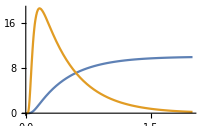

```mathematica
Plot[Evaluate[{pfun[a][t,1],D[pfun[a][t,1],t]}/.a->1],{t,0,2}]
```

```mathematica
param=FindFit[data,pfun[a][t,1],a,t]
```

{a→0.70144}

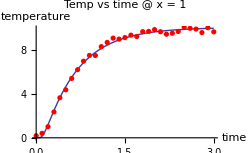

```mathematica
Plot[pfun[a/.param][t,1],{t,0,3},PlotStyle->{Thick,ColorData[1][1]},Epilog->{Red,PointSize[0.015],Point@data},
AxesLabel->{"time","temperature"},PlotLabel->"Temp vs time @ x = 1"]
```

# three modern PDEs

## Shock Waves and Burger’s Equation (DSolve)

```mathematica
BurgersEqn=D[u[t,x],t]+u[t,x]D[u[t,x],x]== ϵ D[u[t,x],x,x];
```

```mathematica
initialCondition=u[0,x]==Piecewise[{{1,x<0}}];
```

```mathematica
dsol=DSolveValue[{BurgersEqn,initialCondition},u[t,x],{t,x}]
```

1/(1+(ⅇ^(-(t-2 x)/(4 ϵ)) (1+Erf[x/(2 √(t ϵ))]))/(1+Erf[(t-x)/(2 √(t ϵ))]))

```mathematica
Table[Plot3D[Evaluate[dsol/.ϵ->j],{x,-2,2},{t,0.001,5},ColorFunction->"CandyColors",PlotPoints->25,ImageSize->Small],{j,{1/10,1/100,1/10000}}]
```

General::munfl: Exp[-10002.2] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9689.9] is too small to represent as a normalized machine number; precision may be lost.

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

## Black Scholes model (DSolve)

```mathematica
BlackScholesModel={D[c[t,s],t]+1/2 s^2 σ^2 D[c[t,s],s,s]+r s D[c[t,s],s]-r c[t,s]==0,c[T,s]==Max[s-k,0]};
```

```mathematica
dsol=DSolveValue[BlackScholesModel,c[t,s],{t,s}]
```

1/2 ⅇ^(-r T) (-ⅇ^(r t) k Erfc[((t-T) (2 r-σ^2)+2 Log[k]-2 Log[s])/(2 √2 √(-t+T) σ)]+ⅇ^(r T) s Erfc[((t-T) (2 r+σ^2)+2 Log[k]-2 Log[s])/(2 √2 √(-t+T) σ)])

```mathematica
dsol/.{t->0,s->100,k->100,σ->0.2,T->1,r-> 0.05}
```

10.4506

```mathematica
FinancialDerivative[{"European","Call"},{"StrikePrice"->100.00,"Expiration"->1},{"InterestRate"-> 0.05,"Volatility"-> 0.2,"CurrentPrice"->100}]
```

10.4506

## Quantum particle in a box (DSolve)

```mathematica
SchrodingerEquation=I ℏ D[ψ[t,x], t]==-ℏ^2/(2 m)D[ψ[t,x], x,x];
```

```mathematica
BC={ψ[t,0]==0,ψ[t,d]==0};
```

```mathematica
IC=ψ[0,x]==1/(√d)Sin[π x/d]+1/(√d)Sin[2π x/d];
```

```mathematica
sol=DSolve[{SchrodingerEquation,BC,IC},ψ[t,x],{t,x}]
```

{{ψ[t,x]→(ⅇ^(-(2 ⅈ π^2 t ℏ)/(d^2 m)) (ⅇ^((3 ⅈ π^2 t ℏ)/(2 d^2 m))+2 Cos[(π x)/d]) Sin[(π x)/d])/(√d)}}

```mathematica
(* computing the probability density *)
```

```mathematica
ρ[t_,x_]=Simplify[ComplexExpand[Conjugate[ψ[t,x]]ψ[t,x]/.First[sol]],d>0]
```

((3+2 Cos[(2 π x)/d]+2 Cos[(π (2 d m x-3 π t ℏ))/(2 d^2 m)]+2 Cos[(π (2 d m x+3 π t ℏ))/(2 d^2 m)]) Sin[(π x)/d]^2)/d

```mathematica
Clear[t,x];
```

```mathematica
ρe[t_,x_]=ρ[t,x]/.{ℏ-> 1.055*^-34,m-> 9.109*^-31,d-> 10^-9}
```

1000000000 (3+2 Cos[1.72444×10^48 (-9.94314×10^-34 t+1.8218×10^-39 x)]+2 Cos[1.72444×10^48 (9.94314×10^-34 t+1.8218×10^-39 x)]+2 Cos[2000000000 π x]) Sin[1000000000 π x]^2

```mathematica
Animate[Plot[ρe[t,x],{x,0,10^-9},PlotRange->{0,4*^9},PlotStyle->ColorData[1][1],ImageSize->Medium,Filling-> Bottom,AxesLabel->{"x(m)","ρe (m^-1)"}],{t,0,3.66*^-15}]
```

# solving PDEs over Regions

## Dirichlet problem in a rectangle (DSolve)

```mathematica
LapEqn=D[u[x,y], x,x]+D[u[x,y], y,y]==0; (* ∇_{x,y}^2 u[x,y]==0 *)
BC=DirichletCondition[u[x,y]==Piecewise[{{UnitTriangle[2x-1],y==0||y==2}},0],True];
Ω=Rectangle[{0,0},{1,2}];
```

```mathematica
sol=FullSimplify[DSolve[{LapEqn,BC},u[x,y],{x,y}∈Ω]]
```

{{u[x,y]→(8 Cosh[π (-1+y) K[1]] Sech[π K[1]] Sin[1/2 π K[1]] Sin[π x K[1]])/(π^2 K[1]^2)K[1]1∞}}

```mathematica
asol=u[x,y]/.sol[[1]]/.{∞->100}//Activate;
```

```mathematica
Plot3D[asol,{x,0,1},{y,0,2},PlotRange->All,ColorFunction->"CandyColors",ImageSize->Small]
```

-Graphics3D-

## Poisson type equations (NDSolve)

```mathematica
Ω=Disk[];
op=-Laplacian[u[x,y],{x,y}]==1;
```

```mathematica
Subscript[Γ, D]=DirichletCondition[u[x,y]==0,x^2+y^2≥0.5];
```

```mathematica
uif=First@NDSolve[{op,Subscript[Γ, D]},u,{x,y}∈Ω]
```

{u→InterpolatingFunction[…]}

```mathematica
Plot3D[Evaluate[u[x,y]/.uif],{x,y}∈Ω,ColorFunction->"CandyColors",Mesh->None,PlotPoints->50,Boxed->False,Axes->False,ImageSize->Small]
```

-Graphics3D-

```mathematica
Ω=ImplicitRegion[0≤x≤5&&0≤y≤10&&!((x-5)^2+(y-5)^2≤3^2),{x,y}];
```

```mathematica
RegionPlot[Ω,AspectRatio->{1,1},ImageSize->Small]
```

-Graphics-

```mathematica
op=-Laplacian[u[x,y],{x,y}]-20;
```

```mathematica
Subscript[Γ, D]={DirichletCondition[u[x,y]==0,x==0&&8≤y≤10],
DirichletCondition[u[x,y]==100,((x-5)^2+(y-5)^2==3^2)]};
```

```mathematica
uif=NDSolveValue[{op==0,Subscript[Γ, D]}, u,{x,y}∈Ω];
```

```mathematica
Plot3D[uif[x,y],{x,y}∈Ω,ColorFunction->"Rainbow",ImageSize->Small]
```

-Graphics3D-

```mathematica
Subscript[Γ, D]=DirichletCondition[u[x,y]==0,x==0&&8≤y≤10];
```

```mathematica
Subscript[Γ, N]=NeumannValue[-2u[x,y],((x-5)^2+(y-5)^2==3^2)];
```

```mathematica
uif=NDSolveValue[{op==Subscript[Γ, N],Subscript[Γ, D]},u,{x,y}∈Ω];
```

```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
Show[
Plot3D[uif[x,y],{x,y}∈uif["ElementMesh"],Mesh->None,ColorFunction->"CandyColors"],
Graphics3D[{Opacity[0.2],EdgeForm[Gray],FaceForm[None],NDSolve`FEM`ElementMeshToGraphicsComplex[uif["ElementMesh"],"CoordinateConversion"->(Join[#,ConstantArray[{0.},{Length[#]}], 2]&)]}],ImageSize->Medium]
```

-Graphics3D-

## some transient problem (NDSolve)

```mathematica
RegionPlot[Ω=ImplicitRegion[y≥0&&(x-3/2)^2+y^2≥ 1/25&&x^2+y^2≥1&&x^2+y^2≤4&&y≤x Tan[π/8],{x,y}],AspectRatio->{1,1},Frame->False,ImageSize->Small]
```

-Graphics-

```mathematica
Clear[eqn,Γ];
```

```mathematica
eqn[t_,x_,y_]=-10Laplacian[u[t,x,y],{x,y}];
```

```mathematica
Subscript[Γ, Dc][t_]={DirichletCondition[u[t,x,y]==200,x^2+y^2==1],
DirichletCondition[u[t,x,y]==10.,x^2+y^2==4]};
```

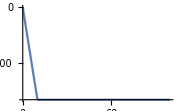

```mathematica
Plot[Piecewise[{{-500.t,t≤10},{-5000,t>10}}],{t,0,100},ImageSize->Small]
```

```mathematica
Subscript[Γ, Nc][t_]=NeumannValue[If[t≤10,-500.t,-5000],(x-3/2)^2+y^2==1/25];
```

```mathematica
unit=NDSolveValue[{eqn[0,x,y]==0,Subscript[Γ, Dc][0]},u[0,x,y],{x,y}∈Ω];
```

```mathematica
Plot3D[unit,{x,y}∈Ω,ColorFunction->"TemperatureMap",ViewPoint->Above,Boxed->False,Axes->False,ImageSize->Tiny]
```

-Graphics3D-

```mathematica
uif=NDSolveValue[{D[u[t,x,y],t]+eqn[t,x,y]==Subscript[Γ, Nc][t],Subscript[Γ, Dc][0],u[0,x,y]==unit},u,{t,0,25},{x,y}∈Ω]
```

InterpolatingFunction[…]

```mathematica
Table[Plot3D[uif[t,x,y],{x,y}∈Ω,ColorFunction->"TemperatureMap",ViewPoint->Above,Boxed->False,Axes->False,ImageSize->Tiny],{t,{0,5,10,15,25}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

# system of PDEs over a region

## Stokes flow in a duct (NDSolve)

```mathematica
ClearAll["Global`*"]
```

```mathematica
(* 
{({{-μ,0},{0,-μ}}.u[x,y]{x,y}Inactive){x,y}Inactive+p^(1,0)[x,y],({{-μ,0},{0,-μ}}.v[x,y]{x,y}Inactive){x,y}Inactive+p^(0,1)[x,y],u^(1,0)[x,y]+v^(0,1)[x,y]}=={0,0,0}/.μ->1
*)
```

```mathematica
ClearAll[iStokesFlow,StokesFlow];
iStokesFlow[a_,depVars:{u_,v_,___,p_},X:{x_,y_,___},msghead_Symbol]:=Module[{diag},
diag=-a*IdentityMatrix[Length[depVars]-1];
Join[(Inactive[Div][diag.Inactive[Grad][#,X],X]&/@Most[depVars])+(D[p,#]&/@X),{Total[MapThread[D[#1,#2]&,{Most[depVars],X}]]}]
];
```

```mathematica
PiecewiseExpand[Piecewise[{{mu,True}}]]
```

mu

```mathematica
StokesFlow[mu_,depVars:{u_,v_,___,p_},X:{x_,y_,___}]/;Length[X]≥2&&Length[depVars]==Length[X]+1:=With[{res=Catch[iStokesFlow[PiecewiseExpand[Piecewise[{{mu,True}}]],depVars,X,StokesFlow],NDSolve`FEM`FEMError[___]]},res/;Unevaluated[res]=!=$Failed
];
```

```mathematica
Ω=ImplicitRegion[0≤x≤2&&0≤y≤0.5&&!(x≥1&&y≤0.1)&&!(x≥1&&y≥0.4),{x,y}];
```

```mathematica
(* programatically generate the PDEs *)
```

```mathematica
pde=StokesFlow[1,{u[x,y],v[x,y],p[x,y]},{x,y}]=={0,0,0}
```

{({{-1,0},{0,-1}}.u[x,y]{x,y}Inactive){x,y}Inactive+p^(1,0)[x,y],({{-1,0},{0,-1}}.v[x,y]{x,y}Inactive){x,y}Inactive+p^(0,1)[x,y],v^(0,1)[x,y]+u^(1,0)[x,y]}=={0,0,0}

```mathematica
(* manually enter the PDEs *)
```

```mathematica
pdes={Inactive[Div][{{-μ,0},{0,-μ}}.Inactive[Grad][u[x,y],{x,y}],{x,y}]+D[p[x,y],x],
Inactive[Div][{{-μ,0},{0,-μ}}.Inactive[Grad][v[x,y],{x,y}],{x,y}]+D[p[x,y],y],
D[u[x,y],x]+D[v[x,y],y]}=={0,0,0}/.μ->1
```

{({{-1,0},{0,-1}}.u[x,y]{x,y}Inactive){x,y}Inactive+p^(1,0)[x,y],({{-1,0},{0,-1}}.v[x,y]{x,y}Inactive){x,y}Inactive+p^(0,1)[x,y],v^(0,1)[x,y]+u^(1,0)[x,y]}=={0,0,0}

```mathematica
Subscript[Γ, D]={
DirichletCondition[u[x,y]==4*0.3*y*(0.5-y)/(0.41)^2,x==0.],
DirichletCondition[{u[x,y]==0.,v[x,y]==0.},0.<x<2],
DirichletCondition[{p[x,y]==0.},x==2]
};
```

```mathematica
{uvel,vvel,pressure}=NDSolveValue[{pdes,Subscript[Γ, D]},{u,v,p},{x,y}∈Ω,Method->{"FiniteElement","InterpolationOrder"->{u-> 2,v-> 2,p->1}}];
```

```mathematica
Show[RegionPlot[Ω,AspectRatio->{1,1}],
VectorPlot[{uvel[x,y],vvel[x,y]},{x,y}∈Ω,VectorStyle->{Opacity[0.75],Black},StreamPoints->12,
StreamColorFunction->"Rainbow",StreamColorFunctionScaling->True]
]
```

-Graphics-

## Structural mechanics (NDSolve)

```mathematica
gr = -Graphics3D-;
```

```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
mesh=ToElementMesh[DiscretizeGraphics@gr,"MeshOrder"->1]
```

ElementMesh[{{-93.9459,93.9356},{0.,890.1},{-102.45,73.6294}},{TetrahedronElement[<175355>]}]

```mathematica
stressOperator[Y_,ν_]:={Inactive[Div][({{0,0,-((Y ν)/((1-2 ν) (1+ν)))},{0,0,0},{-(Y/(2 (1+ν))),0,0}}.Inactive[Grad][w[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{0,-((Y ν)/((1-2 ν) (1+ν))),0},{-(Y/(2 (1+ν))),0,0},{0,0,0}}.Inactive[Grad][v[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{-((Y (1-ν))/((1-2 ν) (1+ν))),0,0},{0,-(Y/(2 (1+ν))),0},{0,0,-(Y/(2 (1+ν)))}}.Inactive[Grad][u[x,y,z],{x,y,z}]),{x,y,z}],Inactive[Div][({{0,0,0},{0,0,-((Y ν)/((1-2 ν) (1+ν)))},{0,-(Y/(2 (1+ν))),0}}.Inactive[Grad][w[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{0,-(Y/(2 (1+ν))),0},{-((Y ν)/((1-2 ν) (1+ν))),0,0},{0,0,0}}.Inactive[Grad][u[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{-(Y/(2 (1+ν))),0,0},{0,-((Y (1-ν))/((1-2 ν) (1+ν))),0},{0,0,-(Y/(2 (1+ν)))}}.Inactive[Grad][v[x,y,z],{x,y,z}]),{x,y,z}],Inactive[Div][({{0,0,0},{0,0,-(Y/(2 (1+ν)))},{0,-((Y ν)/((1-2 ν) (1+ν))),0}}.Inactive[Grad][v[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{0,0,-(Y/(2 (1+ν)))},{0,0,0},{-((Y ν)/((1-2 ν) (1+ν))),0,0}}.Inactive[Grad][u[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{-(Y/(2 (1+ν))),0,0},{0,-(Y/(2 (1+ν))),0},{0,0,-((Y (1-ν))/((1-2 ν) (1+ν)))}}.Inactive[Grad][w[x,y,z],{x,y,z}]),{x,y,z}]};
```

```mathematica
(*specify constraints such that the boundary of the crankshaft is held fixed at these positions *)
```

```mathematica
Subscript[Γ, D]=DirichletCondition[{u[x,y,z]==0.,v[x,y,z]==0.,w[x,y,z]==0.},{y≤ 0.1,y≥890}];
```

```mathematica
(*specify boundary load pushing in the negative z direction*)
```

```mathematica
Subscript[Γ, n]=NeumannValue[-10000.,((217≤y≤256)&&(40≤z≤103))||((584≤y≤ 622)&&(40≤z≤103))];
```

```mathematica
(*solving the coupled PDEs*)
```

```mathematica
AbsoluteTiming[{uif,vif,wif}=NDSolveValue[{stressOperator[10^9,33/100]=={0,0,Subscript[Γ, n]},Subscript[Γ, D]},{u,v,w},{x,y,z}∈mesh];]
```

{5.47197,Null}

```mathematica
Show[
ToBoundaryMesh[mesh]["Wireframe"["MeshElementStyle"-> {Directive[EdgeForm[],FaceForm[Gray]]}]],
ElementMeshDeformation[mesh,{uif,vif,wif},"ScalingFactor"-> 100]["Wireframe"[AspectRatio-> Automatic,"MeshElementStyle"-> Directive[{EdgeForm[],FaceForm[Red]}]]],
ImageSize->200,ViewPoint->{-2,-2,0}
]
```

-Graphics3D-

# symbolic Eigenfunction Problems

## Basic problem (DSolve)

```mathematica
sol=DSolve[{y''[x]+λ y[x]==0,y[0]==0,y[π]==0},y[x],x]
```

{{y[x]→Piecewise[{{C[1] Sin[x √λ], n∈ℤ&&n≥1&&λ==n^2}, {0, True}}]}}

```mathematica
eigfun=Table[y[x]/.sol[[1]]//.{n->i,λ->n^2}/.C[1]->1,{i,5}]
```

{Sin[x],Sin[2 x],Sin[3 x],Sin[4 x],Sin[5 x]}

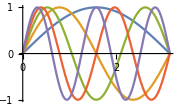

```mathematica
Plot[Evaluate[eigfun],{x,0,π},ImageSize->Small]
```

## Robin problem for an ODE (DSolve)

```mathematica
sol=DSolve[{y''[x]+λ^2 y[x]==0,y[0]+y'[0]==0,y[1]==0},y[x],x]
```

{{y[x]→Piecewise[{{C[1] (-λ Cos[x λ]+Sin[x λ]), λ Cos[λ]==Sin[λ]}, {0, True}}]}}

```mathematica
roots=λ/.Solve[λ Cos[λ]==Sin[λ]&&1<λ<10];
data=Table[{λ,0},{λ,roots}];
```

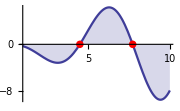

```mathematica
Plot[λ Cos[λ]-Sin[λ],{λ,1,10},Filling->Axis,PlotStyle->ColorData[1][1],Epilog->{Red,PointSize[0.03],Point@data},ImageSize->Small]
```

```mathematica
FindRoot[λ Cos[λ]-Sin[λ]==0,{λ,#}]&/@{4,7}
```

{{λ→4.49341},{λ→7.72525}}

```mathematica
(* we could also have added assumption to DSolve *)
```

```mathematica
dsol=DSolve[{y''[x]+λ^2 y[x]==0,y[0]+y'[0]==0,y[1]==0},y[x],x,Assumptions->1<λ<10]
```

{{y[x]→Piecewise[{{C[1] (-λ Cos[x λ]+Sin[x λ]), λ==Root4.49Root[{-Sin[#1]+Cos[#1] #1&,4.4934094579090641753}]4.493409457909064||λ==Root7.73Root[{-Sin[#1]+Cos[#1] #1&,7.7252518369377071642}]7.725251836937707}, {0, True}}]}}

## Eigenfunction of the Laplacian in a Ball (DEigensystem)

```mathematica
L=-Laplacian[u[x,y,z],{x,y,z}];
```

```mathematica
Β=DirichletCondition[u[x,y,z]==0,True];
```

```mathematica
{vals,funs}=DEigensystem[{L,Β},u[x,y,z],{x,y,z}∈Ball[{0,0,0},2],7];
```

```mathematica
DensityPlot3D[funs[[7]]//N//Evaluate,{x,y,z}∈Ball[{0,0,0},2],Boxed->False,Axes->False,ColorFunction->Hue,ImageSize->Tiny]
```

-Graphics3D-

# NDEigensystem

## eigen modes

-∇_x^2 u =λ u

```mathematica
{vals,funs}=NDEigensystem[-Laplacian[u[x],{x}],u[x],{x,0,Pi},4];
```

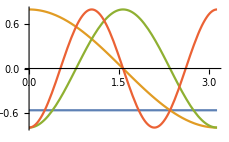

```mathematica
Plot[funs,{x,0,Pi}]
```

```mathematica
{vals,funs}=NDEigensystem[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u[x,y],{x,y}∈Disk[],6];
```

```mathematica
Table[Plot3D[i,{x,y}∈Disk[],ColorFunction->"Rainbow",Mesh->None,PlotPoints->18],{i,funs}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

## car acoustic distribution

```mathematica
img=Import["http://upload.wikimedia.org/wikipedia/commons/d/d3/Mini_cross_section.jpg"];
```

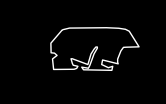
```mathematica
boundary=-Graphics-;
```

```mathematica
region=BoundaryDiscretizeGraphics[boundary,ImageSize->Small];
```

```mathematica
{vals,funs}=NDEigensystem[{-Laplacian[u[x,y],{x,y}]},u[x,y],{x,y}∈region,6];
```

```mathematica
Rasterize[Show[img,ContourPlot[funs[[2]],{x,y}∈region,ColorFunction->Function[x,{Opacity[0.65],ColorData["Rainbow"][x]}]],ImageSize->Small],"Image",ImageSize->200]
```

-Graphics-

# other behaviours of NDSolve/ParametricNDSolve

## using matrix/vector to index inside NDSolve

```mathematica
mat={{1,1},{1,-1}};
```

```mathematica
sol=NDSolve[{x'[t]==mat.x[t],x[0]=={1,2}},x,{t,0,1}]
```

{{x→InterpolatingFunction[…]}}

```mathematica
x[0.5]/.sol
```

{{2.88875,1.97846}}

## putting constraints on the dependent var

```mathematica
NDSolve[{y'[t]==y[t],y[0]==0.01},y,{t,0,10},DependentVariables->{y[t],0,1}]
```

NDSolve::depvoor: Dependent variable(s) y went out of the range specified by {y,0,1} at t = 4.60517.

{{y→InterpolatingFunction[…]}}

```mathematica
NDSolve[{y'[t]==y[t],y[0]==0.01},y,{t,0,10},DependentVariables->{y[t],0,1}:> Echo[t]]
```

4.60517

{{y→InterpolatingFunction[…]}}

## “WhenEvent” in ParametricNDSolve

```mathematica
(*trivial example to check its effect *)
```

```mathematica
sol=ParametricNDSolve[{x'[t]==Sin[t],x[0]==s,WhenEvent[x[t]==1.1,x[t]->x[t]+0.5]},x,{t,0,1},{s}]
```

{x→ParametricFunction[<>]}

```mathematica
pfun=x[1]/.sol
```

InterpolatingFunction[…]

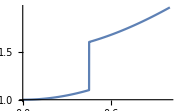

```mathematica
Plot[pfun[t],{t,0,1},ImageSize->Small]
```

## “If” statement in NDSolve

```mathematica
Manipulate[
Module[{a=p[[1]],b=p[[-1]]},
sol=NDSolve[{x'[t]==y[t],y'[t]==If[y[t]-1>0,-1,0.1 y[t]-x[t]],
x[0]==a,y[0]==b},{x,y},{t,0,20}
];
Row[{
ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,20},ImageSize->Small],
Plot[Evaluate[{x[t],y[t]}/.sol],{t,0,20},ImageSize->Small]}
]
],{{p,{0.,0.53}},Locator},SaveDefinitions->True
]
```